#### Soustava rovnic vyplývající z předpokládaného tvaru řešení a podmínek na něj kladených v různých částech oblasti

```mathematica
M = ({{Cosh[a/(2 Subscript[L, 1])], Tanh[Subscript[a, ex]/Subscript[L, 2]]Cosh[a/(2 Subscript[L, 2])]-Sinh[a/(2 Subscript[L, 2])]}, {(-Subscript[D, 1])/Subscript[L, 1] Sinh[a/(2 Subscript[L, 1])], Subscript[D, 2]/Subscript[L, 2] Cosh[a/(2 Subscript[L, 2])]-Subscript[D, 2]/Subscript[L, 2] Tanh[Subscript[a, ex]/Subscript[L, 2]]Sinh[a/(2 Subscript[L, 2])]}});
b = {(S Subscript[L, 1])/(2 Subscript[D, 1])Sinh[a/(2 Subscript[L, 1])],-S/2 Cosh[a/(2 Subscript[L, 1])]};
```

```mathematica
{Subscript[A, 1],Subscript[B, 2]}=LinearSolve[M,b]//FullSimplify
```

{(S L_1 (-Cosh[(a-2 a_ex)/(2 L_2)] Sinh[a/(2 L_1)] D_2 L_1+Cosh[a/(2 L_1)] Sinh[(a-2 a_ex)/(2 L_2)] D_1 L_2))/(2 D_1 (-Cosh[a/(2 L_1)] Cosh[(a-2 a_ex)/(2 L_2)] D_2 L_1+Sinh[a/(2 L_1)] Sinh[(a-2 a_ex)/(2 L_2)] D_1 L_2)),-(S Cosh[a_ex/L_2] L_1 L_2)/(2 Cosh[a/(2 L_1)] Cosh[(a-2 a_ex)/(2 L_2)] D_2 L_1-2 Sinh[a/(2 L_1)] Sinh[(a-2 a_ex)/(2 L_2)] D_1 L_2)}

```mathematica
{Subscript[A, 2],Subscript[B, 1]}={-Subscript[B, 2]Tanh[Subscript[a, ex]/Subscript[L, 2]],-(S Subscript[L, 1])/(2 Subscript[D, 1])}//FullSimplify
```

{(S Sinh[a_ex/L_2] L_1 L_2)/(2 Cosh[a/(2 L_1)] Cosh[(a-2 a_ex)/(2 L_2)] D_2 L_1-2 Sinh[a/(2 L_1)] Sinh[(a-2 a_ex)/(2 L_2)] D_1 L_2),-(S L_1)/(2 D_1)}

#### Předpokládaný průběh neutronového toku

```mathematica
Subscript[ϕ, 1][x_]=Subscript[A, 1] Cosh[x/Subscript[L, 1]]+Subscript[B, 1] Sinh[x/Subscript[L, 1]];
Subscript[ϕ, 2][x_]=Subscript[A, 2] Cosh[x/Subscript[L, 2]]+Subscript[B, 2] Sinh[x/Subscript[L, 2]];
```

#### Ověření předepsaných podmínek

```mathematica
Subscript[ϕ, 2][Subscript[a, ex]]
```

0

```mathematica
Limit[-Subscript[D, 1]D[Subscript[ϕ, 1][x], x],x->0]
```

S/2

```mathematica
Subscript[ϕ, 1][a/2]-Subscript[ϕ, 2][a/2]//FullSimplify
```

0

```mathematica
Limit[Subscript[D, 1] D[Subscript[ϕ, 1][x], x],x->a/2,Direction->1]-Limit[Subscript[D, 2] D[Subscript[ϕ, 2][x], x],x->a/2,Direction->-1]//FullSimplify
```

0

#### Ukázková data

Berylium:

```mathematica
Subscript[D, 1]=0.5;Subscript[L, 1]=21;
```

Voda:

```mathematica
Subscript[D, 2]=0.2;Subscript[L, 2]=2.8;
```

Další parametry:

```mathematica
a=30;Subscript[a, ex]=a+2 Subscript[D, 2];
S=1;
```

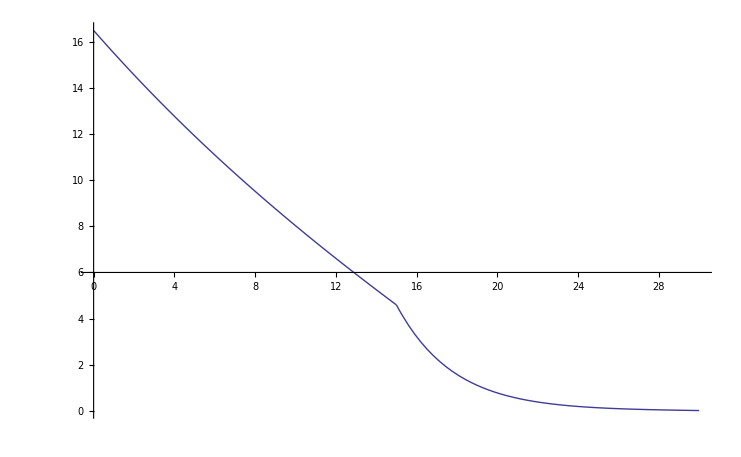

```mathematica
Show[Plot[Subscript[ϕ, 1][x],{x,0,a/2}],Plot[Subscript[ϕ, 2][x],{x,a/2,a}],PlotRange->All]
```

```mathematica
xtest=Table[i/30,{i,0,899}];l=Length[xtest];
ytest=Join[Map[Subscript[ϕ, 1][#]&,xtest[[1;;l/2]]],Map[Subscript[ϕ, 2][#]&,xtest[[l/2+1;;l]]]];
```

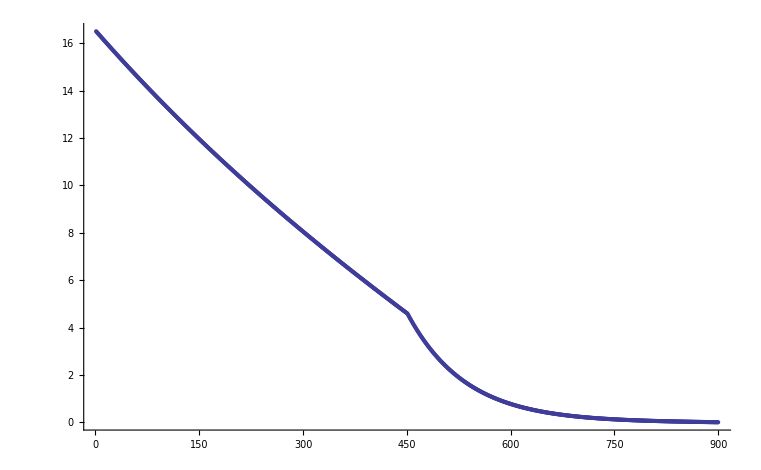

```mathematica
ListPlot[ytest]
```

```mathematica
Export["x.mat", xtest]
```

x.mat

```mathematica
Export["Tok.mat",ytest]
```

Tok.mat

```mathematica
Export["phi0.mat",Subscript[ϕ, 1][0]]
```

phi0.mat